```mathematica
ClearAll["Global`*"];

(*Radiation density*)
OmegaR[h_,Neff_:3.046]:=Module[{Tcmb=2.7255,og,fnu},og=2.472*10^-5*(Tcmb/2.7255)^4;
fnu=1+0.2271*Neff;
(og*fnu)/h^2];

(*Expansion functions*)
E_LCDM[z_,Om_,Or_]:=Sqrt[Om*(1+z)^3+Or*(1+z)^4+(1-Om-Or)];
E_wCDM[z_,Om_,w_,Or_]:=Sqrt[Om*(1+z)^3+Or*(1+z)^4+(1-Om-Or)*(1+z)^(3(1+w))];
E_w0wa[z_,Om_,w0_,wa_,Or_]:=Module[{a=1/(1+z)},Sqrt[Om*(1+z)^3+Or*(1+z)^4+(1-Om-Or)*a^(-3(1+w0+wa))*Exp[-3 wa (1-a)]]];

(*Fiducial params*)
hLCDM=0.674;
OmLCDM=0.315;
OrLCDM=OmegaR[hLCDM];
omegamPlanck=OmLCDM*hLCDM^2;

(*Phantom*)
wPh=-1.22;
hPh=0.74;
OmPh=omegamPlanck/hPh^2;
OrPh=OmegaR[hPh];

(*w0-wa*)
w0DESI=-0.84;
waDESI=-0.59;
hDESI=0.675;
OmDESI=omegamPlanck/hDESI^2;
OrDESI=OmegaR[hDESI];

(*Final E(z) functions*)
E1[z_]:=E_LCDM[z,OmLCDM,OrLCDM];
E2[z_]:=E_wCDM[z,OmPh,wPh,OrPh];
E3[z_]:=E_w0wa[z,OmDESI,w0DESI,waDESI,OrDESI];
```

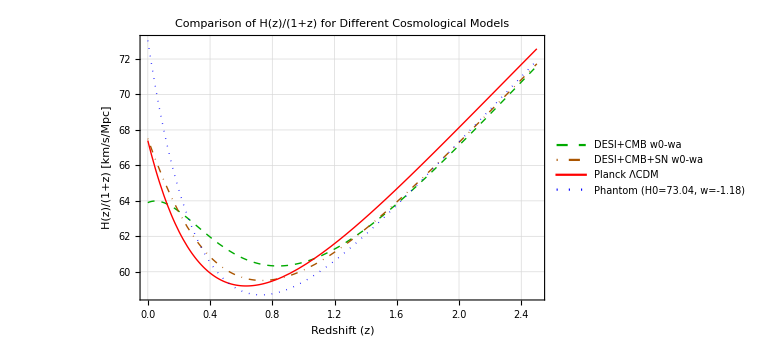

C:\Users\mitso\Downloads\cosmological_models_plot.pdf

```mathematica
(*Mathematica code to plot and compare H(z)/(1+z) for various cosmological models.This version explicitly defines a general wCDM function and uses it to create the ΛCDM and Phantom model curves.*) Hw0waGeneral[z_,H0_,Om_,w0_,wa_]:=Module[{Or=9*^-5},H0*Sqrt[Om*(1+z)^3+Or*(1+z)^4+(1-Om-Or)*(1+z)^(3*(1+w0+wa))*Exp[-3*wa*z/(1+z)]]]


HwCDM[z_,H0_,Om_,w_]:=Module[{Or=9*^-5},H0*Sqrt[Om*(1+z)^3+Or*(1+z)^4+(1-Om-Or)*(1+z)^(3*(1+w))]]




(*1. DESI+CMB best-fit w0-wa Model*)
Hw0waDESI[z_]:=Hw0waGeneral[z,63.9,0.350,-0.45,-1.64]

(*2. DESI+CMB+Pantheon+best-fit w0-wa Model*)
Hw0waDESIsn[z_]:=Hw0waGeneral[z,67.51,0.311,-0.842,-0.59]

(*3. Standard Planck ΛCDM Model (a wCDM case where w=-1)*)
Hlcdm[z_]:=HwCDM[z,67.4,0.315,-1.0]

(*4. Phantom Model consistent with latest SH0ES H0=73.04*)
Hphantom[z_]:=HwCDM[z,73.04,0.268,-1.18]





(*Generate the plot and assign it to a variable*)
comparisonPlot=Plot[{Hw0waDESI[z]/(1+z),Hw0waDESIsn[z]/(1+z),Hlcdm[z]/(1+z),Hphantom[z]/(1+z)},{z,0,2.5},Frame->True,FrameLabel->{Style["Redshift (z)",14],Style["H(z)/(1+z) [km/s/Mpc]",14]},PlotLabel->Style["Comparison of H(z)/(1+z) for Different Cosmological Models",18,Bold],GridLines->Automatic,PlotStyle->{{Thick,Dashed,Darker[Green]},{Thick,DotDashed,Darker[Orange]},{Thick,Red},{Thick,Dotted,Blue}},PlotLegends->Placed[LineLegend[{Style["DESI+CMB w0-wa",12],Style["DESI+CMB+SN w0-wa",12],Style["Planck ΛCDM",12],Style["Phantom (H0=73.04, w=-1.18)",12]},LegendLayout->"Column"],{0.55,0.8}],FrameTicksStyle->Directive[12],ImageSize->Large];

(*Display the plot in the notebook*)
comparisonPlot

(*Export the generated plot to a PDF file in the same directory as the notebook*)
Export[FileNameJoin[{NotebookDirectory[],"cosmological_models_plot.pdf"}],comparisonPlot]
```